I want to write an numerical return amp without precision loss .The precision loss occurs at the Simplify function . I can identify the simplification patterns and write something which does the simplification .
0. Run numerical ReturnAmp for L = 4 without simplification, and see if it gives sensible results
1. See whether such a pattern matching simplification is possible .
2. Run numerical
3. Use memory improvement on ExactReturnAmp

## Preliminaries and Inputs:

```mathematica
Get["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Ising_matrices_package.wl"];
```

```mathematica
DocInnerProd[A_,B_]:=Conjugate[Flatten[A]].Flatten[B]
```

```mathematica
comm[A_,B_]:=A.B-B.A
```

```mathematica
NPrec=20;
```

```mathematica
H={{-2,-1,-1,0,-1,0,0,0},{-1,0,0,-1,0,-1,0,0},{-1,0,2,-1,0,0,-1,0},{0,-1,-1,0,0,0,0,-1},{-1,0,0,0,0,-1,-1,0},{0,-1,0,0,-1,2,0,-1},{0,0,-1,0,-1,0,0,-1},{0,0,0,-1,0,-1,-1,-2}};Operator={{3,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-3}};
```

```mathematica
H4=TFIMHamiltonian[4,1,1];
H5=TFIMHamiltonian[5,1,1];
H6=TFIMHamiltonian[6,1,1];
```

```mathematica
σx4=σx[4];
σx5=σx[5];
σx6=σx[6];
```

```mathematica
σy4=σy[4];
σy5=σy[5];
σy6=σy[6];
```

```mathematica
σz4=σz[4];
σz5=σz[5];
σz6=σz[6];
```

```mathematica
Op={{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}};
```

```mathematica
σx={{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}};
```

```mathematica
σy={{0,-ⅈ,-ⅈ,0,-ⅈ,0,0,0},{ⅈ,0,0,-ⅈ,0,-ⅈ,0,0},{ⅈ,0,0,-ⅈ,0,0,-ⅈ,0},{0,ⅈ,ⅈ,0,0,0,0,-ⅈ},{ⅈ,0,0,0,0,-ⅈ,-ⅈ,0},{0,ⅈ,0,0,ⅈ,0,0,-ⅈ},{0,0,ⅈ,0,ⅈ,0,0,-ⅈ},{0,0,0,ⅈ,0,ⅈ,ⅈ,0}};
```

```mathematica
σz={{3,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-3}};
```

```mathematica
{vals,vecs} = Eigensystem[H];
```

```mathematica
tMax=1000;
tPts=100;
Prec=40;
tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], Prec];
```

## Numerical, with fractions

### As Modules

```mathematica
ReturnAmpFrac[H_,Operator_,NPrec_]:=Module[{U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];//EchoTiming;
Nvals=N[vals,NPrec];Nvecs=N[vecs,NPrec];
CutVals=Table[x=Nvals[[i]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvals]}];
FracVals=Last[Convergents[CutVals[[#]]]]&/@Range[Length@CutVals];
CutVecs=Table[x=Nvecs[[i,j]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}];
FracVecs= Table[Last[Convergents[CutVecs[[i,j]]]],{i,1,Length[CutVecs]}, {j,1,Length[CutVecs]}];
EchoTiming[
U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[FracVals]] . FracVecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];
NNNexpr=Simplify[InnProd];];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFrac2[H_,Operator_,NPrec_]:=Module[{vals,vecs,Nvals,Nvecs,CutVecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];//EchoTiming;
Nvals=N[vals,NPrec];Nvecs=N[vecs,NPrec];
Echo@MatrixForm@Nvecs;
CutVecs=Table[x=Nvecs[[i,j]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}];
FracVecs= Table[Last[Convergents[CutVecs[[i,j]]]],{i,1,Length[CutVecs]}, {j,1,Length[CutVecs]}];
Echo@MatrixForm@FracVecs;
EchoTiming[
U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . FracVecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];];
NNNexpr=Simplify[InnProd];//EchoTiming;
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFrac3[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,CutVecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
{Nvals,Nvecs} = Eigensystem[N[H,NPrec]];
Echo@MatrixForm@Nvecs;
CutVecs=Table[x=Nvecs[[i,j]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}];
FracVecs= Table[Last[Convergents[CutVecs[[i,j]]]],{i,1,Length[CutVecs]}, {j,1,Length[CutVecs]}];
Echo@MatrixForm@CutVecs;
Echo@MatrixForm@FracVecs;
EchoTiming[
U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . FracVecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];
NNNexpr=Simplify[InnProd];];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFrac4[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec+2)];
Echo@MatrixForm@Nvecs;
FracVecs=Table[Rationalize[Nvecs[[i,j]],0],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}];
Echo@MatrixForm@FracVecs;
EchoTiming[U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . FracVecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];];
NNNexpr=Simplify[InnProd];//EchoTiming;
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFrac5[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec+2)];
Echo@MemoryInUse[];
EchoTiming[U=Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];];
Echo@MemoryInUse[];
EchoTiming[NNNexpr=N[Simplify[Rationalize[InnProd,0]],NPrec]];
Echo@MemoryInUse[];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
rationalizeCoefficients[expr_]:=expr/. {a_?NumericQ x_^b_:>Rationalize[a,0] x^b}
```

```mathematica
floatifyCoefficients[expr_]:=expr/. {a_Rational x_^b_:>N[a] x^b}
```

```mathematica
ReturnAmpFrac6[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec+2)];
Echo@MemoryInUse[];
EchoTiming[U=Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];];
Echo@MemoryInUse[];
EchoTiming[NNNexpr=floatifyCoefficients[Simplify[rationalizeCoefficients[InnProd]]]];
Echo@MemoryInUse[];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpNoSimp[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec+2)];
Echo@MemoryInUse[];
EchoTiming[U=Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
NNNexpr=DocInnerProd[Operator,EvolvedOperator];];
Echo@MemoryInUse[];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFullChop[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec-5)];
EchoTiming[U=Chop[Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals],10^(-NPrec-5)];
EvolvedOperator=Chop[Expand@Refine[ConjugateTranspose[U] . Operator . U,t∈Reals],10^(-NPrec+1)];
NNNexpr=Chop[Expand@DocInnerProd[Operator,EvolvedOperator],10^(-NPrec+5)];];
Echo@MemoryInUse[];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpFullChopClear[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,x,FracVecs,U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
Nvecs=Chop[Nvecs,10^(-NPrec-5)];
EchoTiming[U=Chop[Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals],10^(-NPrec-5)];
EvolvedOperator=Chop[Expand@Refine[ConjugateTranspose[U] . Operator . U,t∈Reals],10^(-NPrec+1)];
Clear[U,Nvecs,Nvals];
NNNexpr=Chop[Expand@DocInnerProd[Operator,EvolvedOperator],10^(-NPrec+5)];];
Echo@MemoryInUse[];
Clear[EvolvedOperator];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ReturnAmpJaco[H_,Operator_,NPrec_]:=Module[{Nvals,Nvecs,VecInv},
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H,NPrec]]];
VecInv=Inverse[Nvecs];
Echo@MemoryInUse[];
EchoTiming[
NNNexpr=Chop[Expand[DocInnerProd[Operator,ConjugateTranspose[Nvecs].MatrixExp[-I*t*DiagonalMatrix[Nvals]].ConjugateTranspose[VecInv].Operator.VecInv.MatrixExp[I*t*DiagonalMatrix[Nvals]].Nvecs]],10^(-NPrec+2)]];
Echo@MemoryInUse[];
NNNnorm=NNNexpr/.t->0;
NNNexpr=NNNexpr/NNNnorm]
```

### Expanded

```mathematica
Nvals=N[vals,NPrec];Nvecs=N[vecs,NPrec];
```

```mathematica
CutVals=Table[x=Nvals[[i]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvals]}]
```

{-3.4939592074349341221,3.4939592074349341221,-2.6038754716096765049,2.6038754716096765049,-1,1,0.10991626417474238284,-0.10991626417474238284}

```mathematica
FracVals=Last[Convergents[CutVals[[#]]]]&/@Range[Length@CutVals]
```

{-5481214249/1568768816,5481214249/1568768816,-3965078926/1522760581,3965078926/1522760581,-1,1,689055309/6268911286,-689055309/6268911286}

```mathematica
Select[vecs,(IntegerPart[#]==#)&]
```

{{0,-1.,0,-1.,1.,0,1.,0},{0,1.,0,-1.,-1.,0,1.,0}}

```mathematica
CutVecs=Table[x=Nvecs[[i,j]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}]
```

{{1,0.55495813208737119142,0.38404294326019173926,0.55495813208737119142,0.55495813208737119142,0.38404294326019173926,0.55495813208737119142,1},{-1,1.4450418679126288086,2.6038754716096765049,-1.4450418679126288086,1.4450418679126288086,-2.6038754716096765049,-1.4450418679126288086,1},{-1,-0.24697960371746706105,-0.10991626417474238284,0.24697960371746706105,-0.24697960371746706105,0.10991626417474238284,0.24697960371746706105,1},{1,2.2469796037174670611,-9.097834679044610627,2.2469796037174670611,2.2469796037174670611,-9.097834679044610627,2.2469796037174670611,1},{0,-1,0,-1,1,0,1,0},{0,1,0,-1,-1,0,1,0},{-1,2.8019377358048382525,-3.4939592074349341221,-2.8019377358048382525,2.8019377358048382525,3.4939592074349341221,-2.8019377358048382525,1},{1,-0.80193773580483825247,-0.28620826421558111221,-0.80193773580483825247,-0.80193773580483825247,-0.28620826421558111221,-0.80193773580483825247,1}}

```mathematica
FracVecs= Table[Last[Convergents[CutVecs[[i,j]]]],{i,1,Length[CutVecs]}, {j,1,Length[CutVecs]}]
```

{{1,3045521162/5487839507,1522760581/3965078926,3045521162/5487839507,3045521162/5487839507,1522760581/3965078926,3045521162/5487839507,1},{-1,2257362845/1562143558,3965078926/1522760581,-2257362845/1562143558,2257362845/1562143558,-3965078926/1522760581,-2257362845/1562143558,1},{-1,-1981313435/8022174322,-689055309/6268911286,1981313435/8022174322,-1981313435/8022174322,689055309/6268911286,1981313435/8022174322,1},{1,5487839507/2442318345,-6268911286/689055309,5487839507/2442318345,5487839507/2442318345,-6268911286/689055309,5487839507/2442318345,1},{0,-1,0,-1,1,0,1,0},{0,1,0,-1,-1,0,1,0},{-1,8533360669/3045521162,-5481214249/1568768816,-8533360669/3045521162,8533360669/3045521162,5481214249/1568768816,-8533360669/3045521162,1},{1,-2442318345/3045521162,-1568768816/5481214249,-2442318345/3045521162,-2442318345/3045521162,-1568768816/5481214249,-2442318345/3045521162,1}}

```mathematica
U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . FracVecs,t∈Reals];
```

```mathematica
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
```

```mathematica
InnProdFrac=DocInnerProd[Operator,EvolvedOperator];
```

```mathematica
RetAmpFracExpr=FullSimplify[InnProdFrac];
```

```mathematica
RetAmpFrac=RetAmpFracExpr/(RetAmpFracExpr/.t->0)
```

(ⅇ^(-14.41550188643870602 ⅈ t) (2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968 ⅇ^(7.427583471568837776 ⅈ t)+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^(9.20775094321935301 ⅈ t)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^(10.81162641482902951 ⅈ t)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^(11.9215426790037719 ⅈ t)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^(12.41550188643870602 ⅈ t)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^(13.5254181506134484 ⅈ t)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^(14.19566935808922125 ⅈ t)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^(14.63533441478819079 ⅈ t)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^(15.30558562226396364 ⅈ t)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^(16.41550188643870602 ⅈ t)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^(16.90946109387364014 ⅈ t)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^(18.01937735804838252 ⅈ t)+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^(19.62325282965805903 ⅈ t)+2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968 ⅇ^(21.40342030130857426 ⅈ t)))/7608848048572240656277618418601396546542030462704827424253345625914464754214733269945970325531980440949273790806800

## Numerical, straight up.

```mathematica
Nvals=N[vals,NPrec];Nvecs=N[vecs,NPrec];
```

```mathematica
U=Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals];
```

```mathematica
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
```

```mathematica
InnProd=DocInnerProd[Operator,EvolvedOperator];
```

```mathematica
RetAmpNExpr=FullSimplify[InnProd]
```

1.2 Cos[0.21983252834948477 t]+12. Cos[0.89008373582525762 t]+2. Cos[2. t]+6.2 Cos[2.49395920743493412 t]+2.7 Cos[3.6038754716096765 t]+0.18 Cos[5.20775094321935301 t]+0.015 Cos[6.98791841486986824 t]+0. Sin[0.21983252834948477 t]+0. Sin[0.89008373582525762 t]+0. Sin[2. t]+0. Sin[2.49395920743493412 t]+0. Sin[3.6038754716096765 t]+0. Sin[5.20775094321935301 t]+0. Sin[6.98791841486986824 t]

```mathematica
RetAmpN=RetAmpNExpr/(RetAmpNExpr/.t->0)
```

0.042 (1.2 Cos[0.21983252834948477 t]+12. Cos[0.89008373582525762 t]+2. Cos[2. t]+6.2 Cos[2.49395920743493412 t]+2.7 Cos[3.6038754716096765 t]+0.18 Cos[5.20775094321935301 t]+0.015 Cos[6.98791841486986824 t]+0. Sin[0.21983252834948477 t]+0. Sin[0.89008373582525762 t]+0. Sin[2. t]+0. Sin[2.49395920743493412 t]+0. Sin[3.6038754716096765 t]+0. Sin[5.20775094321935301 t]+0. Sin[6.98791841486986824 t])

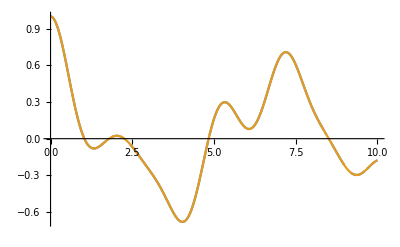

```mathematica
Plot[{RetAmpFrac,RetAmpN},{t,0,10}]
```

## Functions for Lanczos Coeffs, and Probability Amplitudes

```mathematica
(*Generate set with repeated actions of Liouvillian on state Op*)
InitialBasis[H_,Op_,n_,prec_]:=
Module[{B},B=N[NestList[comm[H,#]&,Op,n],prec]]
```

```mathematica
(*Generate Othogonal Basis*)
OrthoBasis[H_,Op_,n_,prec_]:=
Module[{B},B=Orthogonalize[InitialBasis[H,Op,n-1,prec],DocInnerProd, Method->"GramSchmidt",Tolerance->10^(-10)]]
```

```mathematica
(*Extract b_ns from the off-diagonals of the Louivillian in the Krylov Basis*)
LanczosOrthog[H_,Op_,nmax_,prec_]:=
Module[{B,a,b},
B=OrthoBasis[H,Op,nmax,prec];
a=Table[DocInnerProd[B[[n]],comm[H,B[[n]]]],{n,1,nmax-1}];
b=Table[DocInnerProd[B[[n-1]],comm[H,B[[n]]]],{n,2,nmax-1}];
{a,b}]
```

```mathematica
TruncateListRightZeros[list_]:=Module[{pos,backwardslist,len},
backwardslist=Reverse[list];pos=LengthWhile[backwardslist,#==0&];len=Length[list];
If[pos==len,list,Take[list,len-pos]]]
```

```mathematica
list[[1;;-1-LengthWhile[Reverse@list,#==0&]]]
```

{1,2,3,4,5,0,0,1}

```mathematica
AmplitudeCoefficient[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
(*Print[bs=Bs[[1;;-1-LengthWhile[Reverse@Bs,#==0&]]]];*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];
	Genf=F[t];
	(*"The substitution to the function F(t)"*)
	FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts}];
	 ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts}]/.FtoNSwap;
(*"Here we compute the coefficeints cc "*)
	Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*ϕt[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]]
```

## Accuracy Testing

```mathematica
RetAmpcd4=ReturnAmpFullChopClear[TFIMHamiltonian[4,1,1],cd[4],40]
```

0.0068216

2.37042

498776032

0.03125 (2.1481481481481481481481481481481481481+0.08300850062430986902902084780374348594 ⅇ^(-0.36958506180819074540270409514440751174 ⅈ t)+0.08562743490770478838506702960220164573 ⅇ^(0.36958506180819074540270409514440751174 ⅈ t)+0.04360603563256735889388623828531893022 ⅇ^(-0.610814578664557209186266985845481631997 ⅈ t)+0.081794598748336372927878741584672385437 ⅇ^(0.610814578664557209186266985845481631997 ⅈ t)+1.3238255151887537569171006515227160451 ⅇ^(-0.694592710667721395406866507077259184 ⅈ t)+1.0576929017894726314448175397126163726 ⅇ^(0.694592710667721395406866507077259184 ⅈ t)+1.9553278672488210252252661313516529407 ⅇ^(-1.0641777724759121408095706022216666957 ⅈ t)+0.0919429271745456639839676215334128978 ⅇ^(1.0641777724759121408095706022216666957 ⅈ t)+0.59734650166488238080070893349790123672 ⅇ^(-1.305407289332278604593133492922740816 ⅈ t)+0.69181893102297923318341285144043209338 ⅇ^(1.305407289332278604593133492922740816 ⅈ t)+0.32993360745266287028189502602192386957 ⅇ^(-1.389185421335442790813733014154518368 ⅈ t)+0.3357102878694782274373915037859876554 ⅇ^(1.389185421335442790813733014154518368 ⅈ t)+0.094932595939397016641577144081236171804 ⅇ^(-1.389185421335442790813733014154518368 ⅈ t)+0.47357382941549462531511689410061912316 ⅇ^(1.7587704831436335362164371092989258797 ⅈ t)+1.1839828098906511100900036769373808881 ⅇ^(-1.75877048314363353621643710929892587974 ⅈ t)+1.037037037037037037037037037037037037 ⅇ^(-2. ⅈ t)+1.3333333333333333333333333333333333333 ⅇ^(2. ⅈ t)+1.4086558890276991665264313075402789181 ⅇ^(-2.3695850618081907454027040951444075117 ⅈ t)+0.1015524437507294365966523873150059439 ⅇ^(2.3695850618081907454027040951444075117 ⅈ t)+0.3357102878694782274373915037859876554 ⅇ^(-2.45336319381135493162330361637618506375 ⅈ t)+0.11488157147323800746411275917188568909 ⅇ^(2.45336319381135493162330361637618506375 ⅈ t)+0.1517783271946292154456138688340946463 ⅇ^(-2.694592710667721395406866507077259184 ⅈ t)+0.56861965036793525915910672012409785622 ⅇ^(2.694592710667721395406866507077259184 ⅈ t)+2.3346326641694271905505832754516927229 ⅇ^(-3.06417777247591214080957060222166669574 ⅈ t)+1.8344669582458803124459343270841207036 ⅇ^(3.0641777724759121408095706022216666957 ⅈ t)+0.01733004125044607146648943329219135749 ⅇ^(-3.389185421335442790813733014154518368 ⅈ t)+0.39245432069310623004497614456787037199 ⅇ^(3.389185421335442790813733014154518368 ⅈ t)+1.8485808807053877968499888739440036646 ⅇ^(-3.75877048314363353621643710929892587974 ⅈ t)+1.6748751539751523858656494063589245653 ⅇ^(3.75877048314363353621643710929892587974 ⅈ t)+0.091128946108787675815881151297058296749 ⅇ^(-4.12835554495182428161914120444333339149 ⅈ t)+0.00148907109170596582582446228827823531 ⅇ^(4.12835554495182428161914120444333339149 ⅈ t)+0.16986136398942757452119058159628303555 ⅇ^(-4.36958506180819074540270409514440751174 ⅈ t)+0.3357102878694782274373915037859876554 ⅇ^(4.36958506180819074540270409514440751174 ⅈ t)+0.33228350568620555253282995104199267302 ⅇ^(-4.45336319381135493162330361637618506375 ⅈ t)+0.38703684817630788518508240958190489698 ⅇ^(4.45336319381135493162330361637618506375 ⅈ t)+0.08300850062430986902902084780374348594 ⅇ^(-4.82294825561954567702600771152059257549 ⅈ t)+0.11488157147323800746411275917188568909 ⅇ^(4.82294825561954567702600771152059257549 ⅈ t)+1.0783515470935798629429729407689899343 ⅇ^(-5.06417777247591214080957060222166669574 ⅈ t)+0.8399901323340062233434821955311138483 ⅇ^(5.06417777247591214080957060222166669574 ⅈ t)+0.26081070614820674418927036150429217689 ⅇ^(-5.51754096628726707243287421859785175949 ⅈ t)+0.061211246098745900085058027646717422518 ⅇ^(5.51754096628726707243287421859785175949 ⅈ t)+0.42182168227168306632643455607979697659 ⅇ^(-5.75877048314363353621643710929892587974 ⅈ t)+1.1306309795059775193690987949856927437 ⅇ^(5.75877048314363353621643710929892587974 ⅈ t)+0.05514786988475865219891859584217969849 ⅇ^(-6.12835554495182428161914120444333339149 ⅈ t)+0.083008500624309869029020847803743485935 ⅇ^(6.12835554495182428161914120444333339149 ⅈ t)+0.08562743490770478838506702960220164573 ⅇ^(-6.45336319381135493162330361637618506375 ⅈ t)+0.24794787817287857020025431507693552533 ⅇ^(6.45336319381135493162330361637618506375 ⅈ t)+0.54844774510999971525530224014012619614 ⅇ^(-6.82294825561954567702600771152059257549 ⅈ t)+0.18498653121202120686666466734365433484 ⅇ^(6.82294825561954567702600771152059257549 ⅈ t)+0.24794787817287857020025431507693552533 ⅇ^(-7.51754096628726707243287421859785175949 ⅈ t)+0.55702296376021849791464627109169729717 ⅇ^(7.51754096628726707243287421859785175949 ⅈ t)+0.14368093487303025067067476128331344222 ⅇ^(-8.12835554495182428161914120444333339149 ⅈ t)+0.01340163982535369243242016059450411779 ⅇ^(8.12835554495182428161914120444333339149 ⅈ t)+0.16986136398942757452119058159628303555 ⅇ^(-8.82294825561954567702600771152059257549 ⅈ t)+0.24794787817287857020025431507693552533 ⅇ^(8.82294825561954567702600771152059257549 ⅈ t)+0.02897896734980074935436337350047690854 ⅇ^(-9.51754096628726707243287421859785175949 ⅈ t)+0.34559497366139446977475862563678783633 ⅇ^(9.51754096628726707243287421859785175949 ⅈ t))

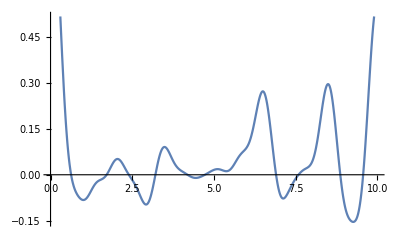

```mathematica
Plot[Re[RetAmpcd4],{t,0,10}]
```

```mathematica
bs=bGen[[2;;]];
```

```mathematica
as=aGen[[2;;]];
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,Re[RetAmpcd4],tVals,Prec];
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}];
ListLinePlot[pPlot]
```

$Aborted

-Graphics-

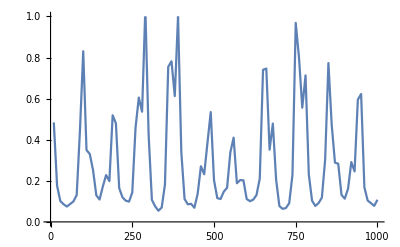

```mathematica
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, 10} ] }, {j, 1, Length[tVals]}];
ListLinePlot[pPlot, PlotRange->{0,1}]
```

```mathematica
{as,bs}=LanczosOrthog[H,σx,12,20]
```

{{0.,0.,0.,0.,0.,0.,0.,0,0,0,0},{2.309401076758503058,4.546060565661951964,2.816999089628490089,3.814750451481857883,0.253176294581603203,2.72912016697930485,0,0,0,0}}

```mathematica
FullSimplify@RetAmpFCC
```

0.7142857142857143+0.007714826084591877 Cos[2.713791735784418888 t]+0.1966630006385962 Cos[3.384042943260191739 t]+0.08133645899109765 Cos[6.097834679044610627 t]+0. ⅈ Sin[2.713791735784418888 t]+0. ⅈ Sin[3.384042943260191739 t]+0. ⅈ Sin[6.097834679044610627 t]

```mathematica
RetAmpJaco=ReturnAmpJaco[H,σx,20]
```

0.0010303

388651216

0.0326316

388656272

0.04166666666666666667 (17.14285714285714286+0.069433434761326891 ⅇ^(-2.713791735784418888 ⅈ t)+0.092577913015102522 ⅇ^(2.713791735784418888 ⅈ t)+0.0231444782537756305 ⅇ^(-2.713791735784418888 ⅈ t)+2.3599560076631543 ⅇ^(-3.384042943260191739 ⅈ t)+2.3599560076631543 ⅇ^(3.384042943260191739 ⅈ t)+0.976037507893171752 ⅇ^(-6.097834679044610627 ⅈ t)+0.976037507893171752 ⅇ^(6.097834679044610627 ⅈ t))

```mathematica
FullSimplify@RetAmpJaco
```

0.1079310130658549 Cos[0.2198325283494847657 t]+0.4781261158152666 Cos[0.890083735825257617 t]+0.342211196322392 Cos[2. t]+0.2557742268328381 Cos[2.493959207434934122 t]+0.1085216493088339 Cos[3.603875471609676505 t]-0.449973164414361 Cos[5.20775094321935301 t]+0.1574089630691756 Cos[6.987918414869868244 t]-0.144825112022774 ⅈ (1. Sin[0.2198325283494847657 t]-0.696360683334382 Sin[0.890083735825257617 t]-2.36292719917648 Sin[2. t]-0.815379301018301 Sin[2.493959207434934122 t]-9.43539570749839 Sin[3.603875471609676505 t]-0.370586203330527 Sin[5.20775094321935301 t]+25.7480199111236 Sin[6.987918414869868244 t])

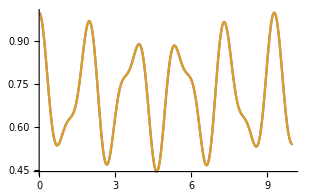

```mathematica
Plot[{RetAmpJaco,RetAmpFCC},{t,0,10}]
```

{2.309401076758503058,4.546060565661951964,2.816999089628490089,3.814750451481857883,0.253176294581603203,2.72912016697930485}

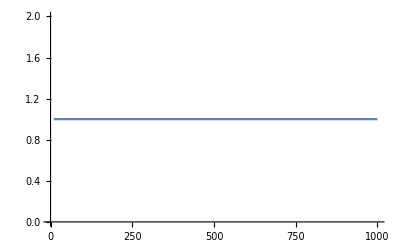

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpJaco,tVals,Prec];
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}];
ListLinePlot[pPlot]
```

```mathematica
RetAmpFrac4=ReturnAmpFrac4[H,σx,20];
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpFrac4,tVals,Prec];
Plot[RetAmpFrac4,{t,0,50}]
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}];
ListLinePlot[pPlot]
```

0.0010701

(0.20449547574694823727 | -0.29550452425305176273 | -0.53248075335263000507 | 0.29550452425305176273 | -0.29550452425305176273 | 0.53248075335263000507 | 0.29550452425305176273 | -0.20449547574694823727
-0.53248075335263000507 | -0.29550452425305176273 | -0.20449547574694823727 | -0.29550452425305176273 | -0.29550452425305176273 | -0.20449547574694823727 | -0.29550452425305176273 | -0.53248075335263000507
-0.6639926388028408839 | -0.1639926388028408839 | -0.07298359029673735844 | 0.1639926388028408839 | -0.1639926388028408839 | 0.07298359029673735844 | 0.1639926388028408839 | 0.6639926388028408839
-0.07298359029673735844 | -0.1639926388028408839 | 0.6639926388028408839 | -0.1639926388028408839 | -0.1639926388028408839 | 0.6639926388028408839 | -0.1639926388028408839 | -0.07298359029673735844
0 | -0.5 | 0 | -0.5 | 0.5 | 0 | 0.5 | 0
0 | -0.5 | 0 | 0.5 | 0.5 | 0 | -0.5 | 0
-0.45949716305589264663 | 0.36848811454978912117 | 0.13151188545021087883 | 0.36848811454978912117 | 0.36848811454978912117 | 0.13151188545021087883 | 0.36848811454978912117 | -0.45949716305589264663
0.13151188545021087883 | -0.36848811454978912117 | 0.45949716305589264663 | 0.36848811454978912117 | -0.36848811454978912117 | -0.45949716305589264663 | 0.36848811454978912117 | -0.13151188545021087883)

(5487839507/26835994718 | -3965078926/13417997359 | -23814052203/44722841254 | 3965078926/13417997359 | -3965078926/13417997359 | 23814052203/44722841254 | 3965078926/13417997359 | -5487839507/26835994718
-23814052203/44722841254 | -3965078926/13417997359 | -5487839507/26835994718 | -3965078926/13417997359 | -3965078926/13417997359 | -5487839507/26835994718 | -3965078926/13417997359 | -23814052203/44722841254
-4011087161/6040860887 | -2670368744/16283467133 | -460953892/6315856621 | 2670368744/16283467133 | -2670368744/16283467133 | 460953892/6315856621 | 2670368744/16283467133 | 4011087161/6040860887
-460953892/6315856621 | -2670368744/16283467133 | 4011087161/6040860887 | -2670368744/16283467133 | -2670368744/16283467133 | 4011087161/6040860887 | -2670368744/16283467133 | -460953892/6315856621
0 | -1/2 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2 | 1/2 | 0 | -1/2 | 0
-4388971030/9551682541 | 5481214249/14874873931 | 1522760581/11578881831 | 5481214249/14874873931 | 5481214249/14874873931 | 1522760581/11578881831 | 5481214249/14874873931 | -4388971030/9551682541
1522760581/11578881831 | -5481214249/14874873931 | 4388971030/9551682541 | 5481214249/14874873931 | -5481214249/14874873931 | -4388971030/9551682541 | 5481214249/14874873931 | -1522760581/11578881831)

0.0489994

0.258692

{2.309401076758503058,4.546060565661951964,2.816999089628490089,3.814750451481857883,0.253176294581603203,2.72912016697930485}

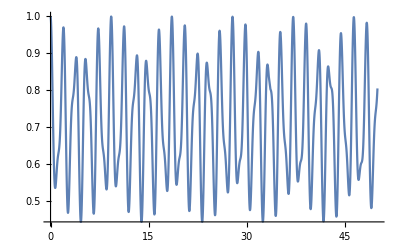

-Graphics-

```mathematica
RetAmpFrac5=ReturnAmpFrac5[H,σx,20];
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpFrac5,tVals,Prec];
Plot[RetAmpFrac5,{t,0,50}]
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}];
ListLinePlot[pPlot]
```

0.0016795

(0.20449547574694823727 | -0.29550452425305176273 | -0.53248075335263000507 | 0.29550452425305176273 | -0.29550452425305176273 | 0.53248075335263000507 | 0.29550452425305176273 | -0.20449547574694823727
-0.53248075335263000507 | -0.29550452425305176273 | -0.20449547574694823727 | -0.29550452425305176273 | -0.29550452425305176273 | -0.20449547574694823727 | -0.29550452425305176273 | -0.53248075335263000507
-0.6639926388028408839 | -0.1639926388028408839 | -0.07298359029673735844 | 0.1639926388028408839 | -0.1639926388028408839 | 0.07298359029673735844 | 0.1639926388028408839 | 0.6639926388028408839
-0.07298359029673735844 | -0.1639926388028408839 | 0.6639926388028408839 | -0.1639926388028408839 | -0.1639926388028408839 | 0.6639926388028408839 | -0.1639926388028408839 | -0.07298359029673735844
0 | -0.5 | 0 | -0.5 | 0.5 | 0 | 0.5 | 0
0 | -0.5 | 0 | 0.5 | 0.5 | 0 | -0.5 | 0
-0.45949716305589264663 | 0.36848811454978912117 | 0.13151188545021087883 | 0.36848811454978912117 | 0.36848811454978912117 | 0.13151188545021087883 | 0.36848811454978912117 | -0.45949716305589264663
0.13151188545021087883 | -0.36848811454978912117 | 0.45949716305589264663 | 0.36848811454978912117 | -0.36848811454978912117 | -0.45949716305589264663 | 0.36848811454978912117 | -0.13151188545021087883)

0.0585455

0.343301

{2.309401076758503058,4.546060565661951964,2.816999089628490089,3.814750451481857883,0.253176294581603203,2.72912016697930485}

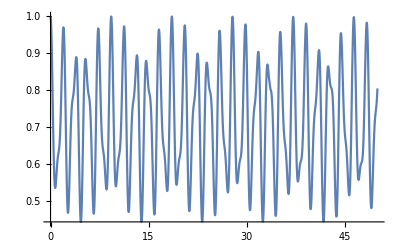

-Graphics-

## Efficiency Testing

```mathematica
ReturnAmpFrac2[H,Operator,20]
```

0.0783876

(ⅇ^(-14.41550188643870602 ⅈ t) (2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968 ⅇ^(7.427583471568837776 ⅈ t)+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^(9.20775094321935301 ⅈ t)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^(10.81162641482902951 ⅈ t)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^(11.9215426790037719 ⅈ t)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^(12.41550188643870602 ⅈ t)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^(13.5254181506134484 ⅈ t)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^(14.19566935808922125 ⅈ t)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^(14.63533441478819079 ⅈ t)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^(15.30558562226396364 ⅈ t)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^(16.41550188643870602 ⅈ t)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^(16.90946109387364014 ⅈ t)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^(18.01937735804838252 ⅈ t)+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^(19.62325282965805903 ⅈ t)+2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968 ⅇ^(21.40342030130857426 ⅈ t)))/7608848048572240656277618418601396546542030462704827424253345625914464754214733269945970325531980440949273790806800

```mathematica
ReturnAmpFrac[H,Operator,20]
```

0.0967286

0.0298754

(ⅇ^(-(5481214249 ⅈ t)/784384408) (2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^((2126284822305147053 ⅈ t)/1194429656853421048)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^((16640138692640835035 ⅈ t)/4917236267873628688)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^((16824874457994877423157956539 ⅈ t)/3743886778090759227758573864)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^((3912445433 ⅈ t)/784384408)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^((14566869166480290285 ⅈ t)/2388859313706842096)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^((16640138692640835035 ⅈ t)/2458618133936814344)+195291099426180877037772085842270496868456455412573678633261949869685175407282838529236481828560002889976982303280 ⅇ^((17721107173899279179 ⅈ t)/2458618133936814344)+1858704986186403028168321683505647359462029660325775485597248814261129758710680369409895480328826048925248116799177 ⅇ^((18819438811090584391 ⅈ t)/2388859313706842096)+317035335357176694011567434108391522772584602612701142677222734413102698092280552914415430230499185039553074616950 ⅇ^((7049983065 ⅈ t)/784384408)+981202854823248480729394551200938849718952259433784792702950788863192903281577173608496714075358311230791704108673 ⅇ^((35499076261621595357159041795 ⅈ t)/3743886778090759227758573864)+421027036949880200925226626387582315687822225425169172834038262051900398359032588262180922772398610249368954702507 ⅇ^((52082353040439393393 ⅈ t)/4917236267873628688)+28803285500356618113440548132671844612961757833701223514995162067782734422793086108397697989952953616350873228845 ⅇ^((14566869166480290285 ⅈ t)/1194429656853421048)+2359426042874429153086280123195884148208270308708216166955101430438708833720026140362435540395108523347189643968 ⅇ^((5481214249 ⅈ t)/392192204)))/7608848048572240656277618418601396546542030462704827424253345625914464754214733269945970325531980440949273790806800

```mathematica
list={1,2,3,4,5,0,0,1,0,0};
```

```mathematica
truncatedList=FirstCase[SplitBy[list,#!=0&],{___,Except[0]}]
```

{1,2,3,4,5}

```mathematica
truncateListRightZeros[list_]:=Module[{pos},pos=LengthWhile[list,#!=0&];
If[pos==Length[list],list,Take[list,pos]]]

truncatedList=truncateListRightZeros[list]
```

{1,2,3,4,5}

```mathematica
truncateListRightZeros[list_]:=Module[{pos,backwardslist,len},
backwardslist=Reverse[list];pos=LengthWhile[backwardslist,#==0&];len=Length[list];
If[pos==len,list,Take[list,len-pos]]]
```

```mathematica
truncateListRightZeros[list]
```

{1,2,3,4,5,0,0,1}

```mathematica
EchoTiming@Eigensystem[H5]
```

14.8794

{{Root-6.03Root[1+25 #1+30 #1^2-26 #1^3+#1^4+#1^5&,1]-6.02667418333227,Root6.03Root[-1+25 #1-30 #1^2-26 #1^3-#1^4+#1^5&,5]6.02667418333227,Root-5.46Root[-89+25 #1+58 #1^2-26 #1^3-#1^4+#1^5&,1]-5.45741483023913,Root5.46Root[89+25 #1-58 #1^2-26 #1^3+#1^4+#1^5&,5]5.45741483023913,Root-4.37Root[23+45 #1-26 #1^2-14 #1^3+3 #1^4+#1^5&,1]-4.365014131324725,Root4.37Root[-23+45 #1+26 #1^2-14 #1^3-3 #1^4+#1^5&,5]4.365014131324725,Root3.80Root[-89+25 #1+58 #1^2-26 #1^3-#1^4+#1^5&,5]3.795754778231584,Root-3.80Root[89+25 #1-58 #1^2-26 #1^3+#1^4+#1^5&,1]-3.795754778231584,Root3.41Root[1+25 #1+30 #1^2-26 #1^3+#1^4+#1^5&,5]3.40723124755113,Root-3.41Root[-1+25 #1-30 #1^2-26 #1^3-#1^4+#1^5&,1]-3.40723124755113,Root-2.84Root[-23+45 #1+26 #1^2-14 #1^3-3 #1^4+#1^5&,1]-2.8379718944579895,Root2.84Root[23+45 #1-26 #1^2-14 #1^3+3 #1^4+#1^5&,5]2.8379718944579895,Root-2.66Root[23+45 #1-26 #1^2-14 #1^3+3 #1^4+#1^5&,2]-2.6616600520075457,Root2.66Root[-23+45 #1+26 #1^2-14 #1^3-3 #1^4+#1^5&,4]2.6616600520075457,Root-2.19Root[-1+25 #1-30 #1^2-26 #1^3-#1^4+#1^5&,2]-2.1887022888742806,Root2.19Root[1+25 #1+30 #1^2-26 #1^3+#1^4+#1^5&,4]2.1887022888742806,Root2.09Root[-89+25 #1+58 #1^2-26 #1^3-#1^4+#1^5&,4]2.092400698914405,Root-2.09Root[89+25 #1-58 #1^2-26 #1^3+#1^4+#1^5&,2]-2.092400698914405,Root-1.75Root[89+25 #1-58 #1^2-26 #1^3+#1^4+#1^5&,3]-1.7455711955435844,Root1.75Root[-89+25 #1+58 #1^2-26 #1^3-#1^4+#1^5&,3]1.7455711955435844,Root-1.62Root[-23+45 #1+26 #1^2-14 #1^3-3 #1^4+#1^5&,2]-1.6194429357811402,Root1.62Root[23+45 #1-26 #1^2-14 #1^3+3 #1^4+#1^5&,4]1.6194429357811402,Root-1.18Root[-89+25 #1+58 #1^2-26 #1^3-#1^4+#1^5&,2]-1.176311842450444,Root1.18Root[89+25 #1-58 #1^2-26 #1^3+#1^4+#1^5&,4]1.176311842450444,-1,1,Root-0.527Root[1+25 #1+30 #1^2-26 #1^3+#1^4+#1^5&,2]-0.5270422368667351,Root0.527Root[-1+25 #1-30 #1^2-26 #1^3-#1^4+#1^5&,4]0.5270422368667351,Root-0.431Root[23+45 #1-26 #1^2-14 #1^3+3 #1^4+#1^5&,3]-0.4307406469068594,Root0.431Root[-23+45 #1+26 #1^2-14 #1^3-3 #1^4+#1^5&,3]0.4307406469068594,Root-0.0422Root[1+25 #1+30 #1^2-26 #1^3+#1^4+#1^5&,3]-0.04221711622640545,Root0.0422Root[-1+25 #1-30 #1^2-26 #1^3-#1^4+#1^5&,3]0.04221711622640545},{{1,Root0.521Root[-1+#1+4 #1^2-3 #1^3-3 #1^4+#1^5&,3]0.5211085581132027,Root0.334Root[-23+15 #1+119 #1^2+116 #1^3+35 #1^4+#1^5&,5]0.333660572324947,Root0.433Root[1-6 #1+10 #1^2-#1^3-6 #1^4+#1^5&,3]0.4329526368879808,Root0.317Root[43+25 #1-382 #1^2-378 #1^3-45 #1^4+#1^5&,4]0.317135922455971,Root0.198Root[23-129 #1+52 #1^2+73 #1^3-21 #1^4+#1^5&,2]0.1983115430148835,Root0.257Root[-1+#1+15 #1^2-14 #1^3-3 #1^4+#1^5&,3]0.25732589522144905,Root0.433Root[1-6 #1+10 #1^2-#1^3-6 #1^4+#1^5&,3]0.4329526368879808,Root0.334Root[-23+15 #1+119 #1^2+116 #1^3+35 #1^4+#1^5&,5]0.333660572324947,Root0.186Root[23-120 #1-26 #1^2+41 #1^3+14 #1^4+#1^5&,4]0.18649029889315946,Root0.134Root[-1+9 #1-6 #1^2-42 #1^3+7 #1^4+#1^5&,3]0.13409472622403842,Root0.198Root[23-129 #1+52 #1^2+73 #1^3-21 #1^4+#1^5&,2]0.1983115430148835,Root0.257Root[-1+#1+15 #1^2-14 #1^3-3 #1^4+#1^5&,3]0.25732589522144905,Root0.186Root[23-120 #1-26 #1^2+41 #1^3+14 #1^4+#1^5&,4]0.18649029889315946,Root0.281Root[-89+397 #1-282 #1^2-14 #1^3+19 #1^4+#1^5&,3]0.28057989887191376,Root0.521Root[-1+#1+4 #1^2-3 #1^3-3 #1^4+#1^5&,3]0.5211085581132027,Root0.521Root[-1+#1+4 #1^2-3 #1^3-3 #1^4+#1^5&,3]0.5211085581132027,Root0.281Root[-89+397 #1-282 #1^2-14 #1^3+19 #1^4+#1^5&,3]0.28057989887191376,Root0.186Root[23-120 #1-26 #1^2+41 #1^3+14 #1^4+#1^5&,4]0.18649029889315946,Root0.257Root[-1+#1+15 #1^2-14 #1^3-3 #1^4+#1^5&,3]0.25732589522144905,Root0.198Root[23-129 #1+52 #1^2+73 #1^3-21 #1^4+#1^5&,2]0.1983115430148835,Root0.134Root[-1+9 #1-6 #1^2-42 #1^3+7 #1^4+#1^5&,3]0.13409472622403842,Root0.186Root[23-120 #1-26 #1^2+41 #1^3+14 #1^4+#1^5&,4]0.18649029889315946,Root0.334Root[-23+15 #1+119 #1^2+116 #1^3+35 #1^4+#1^5&,5]0.333660572324947,Root0.433Root[1-6 #1+10 #1^2-#1^3-6 #1^4+#1^5&,3]0.4329526368879808,Root0.257Root[-1+#1+15 #1^2-14 #1^3-3 #1^4+#1^5&,3]0.25732589522144905,Root0.198Root[23-129 #1+52 #1^2+73 #1^3-21 #1^4+#1^5&,2]0.1983115430148835,Root0.317Root[43+25 #1-382 #1^2-378 #1^3-45 #1^4+#1^5&,4]0.317135922455971,Root0.433Root[1-6 #1+10 #1^2-#1^3-6 #1^4+#1^5&,3]0.4329526368879808,Root0.334Root[-23+15 #1+119 #1^2+116 #1^3+35 #1^4+#1^5&,5]0.333660572324947,Root0.521Root[-1+#1+4 #1^2-3 #1^3-3 #1^4+#1^5&,3]0.5211085581132027,1},31}}
 |  |  |  |

```mathematica
EchoTiming@Eigensystem[N[H5,1000]]
```

0.663743

{{1029,-1029,-1029,1027,-1029,1028,1029,-1029,-1029,1029,1029,-1029,1029,-1029,1029,-1029,-1029,1029,1028,-1029,1029,-1029,1029,-1029,1029,-1029,1029,-1029,-1029,1029,1029,-1029},{1}}
 |  |  |  |

```mathematica
y
```

0.8712010837480137848014

```mathematica
list=Join[{0,1,1.},Table[N[y,i],{i,1,17}]]
```

{0,1,1.,0.9,0.87,0.871,0.8712,0.8712,0.871201,0.8712011,0.87120108,0.871201084,0.8712010837,0.87120108375,0.871201083748,0.871201083748,0.87120108374801,0.871201083748014,0.8712010837480138,0.87120108374801378}

```mathematica
EchoTiming[FracVecs= Table[Last[Convergents[list[[i]]]],{i,1,Length[list]}]]
```

ContinuedFraction::start: Warning: ContinuedFraction was unable to obtain at least one term using precision 15.9546.

0.0020032

{0,1,1.,1,1,7/8,27/31,115/132,115/132,602/691,602/691,16741/19216,16741/19216,34084/39123,34084/39123,34084/39123,1652773/1897120,1652773/1897120,26478452/30393043,26478452/30393043}

```mathematica
EchoTiming[FracVecs2= Table[Rationalize[list[[i]],0],{i,1,Length[list]}]]
```

0.0001471

{0,1,1,6/7,7/8,27/31,115/132,487/559,602/691,602/691,16741/19216,34084/39123,34084/39123,1652773/1897120,1652773/1897120,1652773/1897120,26478452/30393043,26478452/30393043,54609677/62683206,54609677/62683206}

```mathematica
list-FracVecs2
```

{0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
list-FracVecs
```

{0,0,0.,-0.1,-0.1,-0.004,0.0002,-0.00001,-0.00001,0.,-7.×10^-8,1.×10^-9,1.×10^-9,-1.×10^-11,-1.×10^-11,-1.3×10^-11,2.×10^-14,2.×10^-14,-5.×10^-16,-5.×10^-16}

```mathematica
expr= 0.300000t^(730861)+9.8672960736t^(97639)+0.05865965t^(976297);
```

```mathematica
Rationalize[expr]
```

9.8673 t^97639+(3 t^730861)/10+0.0586597 t^976297

```mathematica
Rationalize[expr,0]
```

(175324692 t^97639)/17768261+(3 t^730861)/10+(1173193 t^976297)/20000000

```mathematica
list={0,1,2,3,4}
```

{0,1,2,3,4}

```mathematica
ParallelMap[Sin,list]
```

{0,Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
F[M_]:=Integrate[x^i+i^x,{x,1,300}]

Ops=Table[i,{i,1,30}];
RAs=ParallelMap[F[#]&,Ops]//AbsoluteTiming;
Print[RAs]

RAs=Map[F[#]&,Ops]//AbsoluteTiming;
Print[RAs]
```

{0.847881,{(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i]}}

{4.38566,{(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i],(-1+300^(1+i))/(1+i)+(i (-1+i^299))/Log[i]}}

## Memory Efficiency Testing

1. Decrease memory usage.
1.1 Only Rationalize the constant prefactor of the exponential.
1.2 Try ToPackedArray.
1.3 Clear variables from memory after use

2. Simplify the expression with the Expand, Group, Parallel Simplify trick.

### Rationalizing the prefactor

```mathematica
expr=0.8367082Exp[0.08038I*t] +0.00973972Exp[0.67392*I*t] +Exp[0.8320*I*t] +0.003Exp[0.8320*I*t];
```

```mathematica
rat=Rationalize[expr,0]
```

(4183541 ⅇ^((4019 ⅈ t)/50000))/5000000+(243493 ⅇ^((2106 ⅈ t)/3125))/25000000+(1003 ⅇ^((104 ⅈ t)/125))/1000

```mathematica
rationalizeCoefficients[expr_]:=expr/. {a_?NumericQ x_^b_:>Rationalize[a,0] x^b}
```

```mathematica
floatifyCoefficients[expr_]:=expr/. {a_Rational x_^b_:>N[a] x^b}
```

```mathematica
convertToFloats[expr_]:=expr/. {a_Rational x_^b_:>N[a] x^b,Exp[c_]:>Exp[N[c]]}
```

```mathematica
rationalizeCoefficients[expr]
```

(4183541 ⅇ^((0.+0.08038 ⅈ) t))/5000000+(243493 ⅇ^((0.+0.67392 ⅈ) t))/25000000+(1003 ⅇ^((0.+0.832 ⅈ) t))/1000

```mathematica
floatifyCoefficients[rationalizeCoefficients[expr]]//EchoTiming
```

0.0001225

0.836708 ⅇ^((0.+0.08038 ⅈ) t)+0.00973972 ⅇ^((0.+0.67392 ⅈ) t)+1.003 ⅇ^((0.+0.832 ⅈ) t)

```mathematica
convertToFloats[expr]//EchoTiming
```

0.0001186

0.836708 ⅇ^((0.+0.08038 ⅈ) t)+0.00973972 ⅇ^((0.+0.67392 ⅈ) t)+1.003 ⅇ^((0.+0.832 ⅈ) t)

```mathematica
exprFrom5=ReturnAmpFrac5[H4,σx4,20]//ByteCount
```

0.0297528

296714376

0.725239

314772704

2.80897

314772784

45888

```mathematica
ReturnAmpFrac6[H4,σx4,20]//ByteCount
```

0.0063319

297186936

0.573766

315245816

18.3713

316082664

18088

```mathematica
ReturnAmpNoSimp[H4,σx4,20]//ByteCount
```

0.0059996

329219824

0.579695

347290088

10346720

### Chopping at different points

```mathematica
NPrec=15;
EchoTiming[{Nvals,Nvecs} = Eigensystem[N[H4,NPrec]]];Nvecs=Chop[Nvecs,10^(-NPrec-5)];
```

0.0079972

```mathematica
EchoTiming[U=Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals]]//ByteCount
```

0.0182241

1308888

```mathematica
EchoTiming[UChopped=Chop[Refine[Inverse[Nvecs] . MatrixExp[I*t*DiagonalMatrix[Nvals]] . Nvecs,t∈Reals],10^(-NPrec-5)]]//ByteCount
```

0.0241595

1166104

```mathematica
Operator=σx4;
```

```mathematica
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals]//ByteCount
```

39680488

```mathematica
ChoppedEvolvedOperator=Chop[Expand[Refine[ConjugateTranspose[U] . Operator . U,t∈Reals]],10^(-NPrec+1)]//ByteCount
```

884872

```mathematica
ChopChoppedEvolvedOperator=Chop[Expand[Refine[ConjugateTranspose[UChopped] . Operator . UChopped,t∈Reals]],10^(-NPrec+1)]
```

{1}
 |  |  |  |

```mathematica
NNNexprChop=Chop[Expand@DocInnerProd[Operator,ChopChoppedEvolvedOperator],10^(-NPrec+5)];
NNNnorm = NNNexprChop/.t->0;
NNNexprChop=NNNexprChop/ NNNnorm;
```

```mathematica
FullNNNexpr=ReturnAmpNoSimp[H4,σx4,15]
```

0.0282397

667987496

0.727371

685416784

0.015625 ((0.018130656796282 ⅇ^(-0.30540728933228 ⅈ t)-0.027777777777778 ⅇ^1+16+0.079982923376995 ⅇ^(-59 ⅈ t)) (1)+1022+(1) (1))
 |  |  |  |

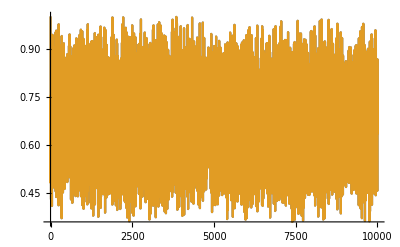

```mathematica
Plot[{NNNexprChop,FullNNNexpr},{t,0,10000}]
```

```mathematica
Plot[NNNexprChop-FullNNNexpr,{t,0,10000}]
```

-Graphics-

```mathematica
NNNexprChop//ByteCount
```

5104

```mathematica
FullNNNexpr//ByteCount
```

10048544

```mathematica
NNNexprChop
```

0.015625 (42.666666666667+0.033444139824 ⅇ^(-1.7587704831436 ⅈ t)+0.033444139824 ⅇ^(1.7587704831436 ⅈ t)+0.358559500068 ⅇ^(-2.3695850618082 ⅈ t)+0.358559500068 ⅇ^(2.3695850618082 ⅈ t)+5.396187756135 ⅇ^(-2.6945927106677 ⅈ t)+5.396187756135 ⅇ^(2.6945927106677 ⅈ t)+0.152754252463 ⅇ^(-4.4533631938114 ⅈ t)+0.152754252463 ⅇ^(4.4533631938114 ⅈ t)+3.459256992931 ⅇ^(5.0641777724759 ⅈ t)+3.459256992931 ⅇ^(-5.0641777724759 ⅈ t)+1.266464025246 ⅇ^(-6.8229482556195 ⅈ t)+1.266464025246 ⅇ^(6.8229482556195 ⅈ t))

```mathematica
RetAmp5=ReturnAmpFullChop[H5,σx5,20];
```

0.0469494

112.436

715751352

```mathematica
RetAmp5//ByteCount
```

8248

```mathematica
RetAmp5
```

0.00625 (101.8181818181818182+0.0184016643285328 ⅇ^(1.2185289586768493 ⅈ t)+0.0184016643285328 ⅇ^(-1.2185289586768493 ⅈ t)+0.1620064208068924 ⅇ^(-1.70335407931717897 ⅈ t)+0.1620064208068924 ⅇ^(1.70335407931717897 ⅈ t)+0.93150710612173903 ⅇ^(-2.05018358268799969 ⅈ t)+0.93150710612173903 ⅇ^(2.05018358268799969 ⅈ t)+11.498092914259484 ⅇ^(-2.230919405100686264 ⅈ t)+11.498092914259484 ⅇ^(2.230919405100686264 ⅈ t)+0.06776425890976898 ⅇ^(-3.268712541364848998 ⅈ t)+0.06776425890976898 ⅇ^(3.268712541364848998 ⅈ t)+0.62012295430018571 ⅇ^(-3.934273484417865237 ⅈ t)+0.62012295430018571 ⅇ^(3.934273484417865237 ⅈ t)+8.71962317167810483 ⅇ^(-4.281102987788685958 ⅈ t)+8.71962317167810483 ⅇ^(4.281102987788685958 ⅈ t)+0.23469717406945153 ⅇ^(-5.499631946465535262 ⅈ t)+0.23469717406945153 ⅇ^(5.499631946465535262 ⅈ t)+5.08323074758780057 ⅇ^(-5.984457067105864932 ⅈ t)+5.08323074758780057 ⅇ^(5.984457067105864932 ⅈ t)+1.7554626788471312 ⅇ^(-7.202986025782714235 ⅈ t)+1.7554626788471312 ⅇ^(7.202986025782714235 ⅈ t))

```mathematica
EchoTiming[ReturnAmpFullChop[H4,σx4,20]//ByteCount]
```

0.0086136

3.14014

705347080

3.253

5088

```mathematica
EchoTiming[ReturnAmpFullChopClear[H4,σx4,20]//ByteCount]
```

0.0059372

706009656

704253008

2.97177

704252792

703422504

3.13656

5088

### Grouping and parallelizing the simplification

```mathematica
UnSimplifiedExpr=ReturnAmpNoSimp[H4,σx4,20];
```

0.0096946

528279600

0.553665

546056168

```mathematica
ChoppedExpr=ReturnAmpChop[H4,σx4,20]
```

0.0061526

541144576

1.13745

559754224

0.015625 (42.66666666666666667+0.03344413982356805 ⅇ^(-1.75877048314363354 ⅈ t)+0.03344413982356805 ⅇ^(1.75877048314363354 ⅈ t)+0. ⅇ^(-2. ⅈ t)+0.35855950006832684 ⅇ^(-2.369585061808190745 ⅈ t)+0.35855950006832684 ⅇ^(2.369585061808190745 ⅈ t)+5.3961877561348114 ⅇ^(-2.6945927106677214 ⅈ t)+5.3961877561348114 ⅇ^(2.6945927106677214 ⅈ t)+0.15275425246307606 ⅇ^(-4.453363193811354932 ⅈ t)+0.15275425246307606 ⅇ^(4.453363193811354932 ⅈ t)+3.45925699293050944 ⅇ^(-5.064177772475912141 ⅈ t)+3.45925699293050944 ⅇ^(5.064177772475912141 ⅈ t)+1.26646402524637488 ⅇ^(-6.822948255619545677 ⅈ t)+1.26646402524637488 ⅇ^(6.822948255619545677 ⅈ t))

```mathematica
Plot[ChoppedExpr-UnSimplifiedExpr,{t,0,10000}]
```

-Graphics-

```mathematica
Echo[MemoryAvailable[],"Memory available for current kernel session: "]
```

Memory available for current kernel session:   993124352

993124352

```mathematica
Expand[UnSimplifiedExpr]
```

0.636363636363636364 ⅇ^(0. ⅈ t)+0. ⅇ^(-0.08443423245281089178 ⅈ t)+0. ⅇ^(0.08443423245281089178 ⅈ t)+0. ⅇ^(-0.096301589959875678 ⅈ t)+0. ⅇ^(0.0963015899598756777 ⅈ t)+0. ⅇ^(-0.12612825976244416 ⅈ t)+0. ⅇ^(0.12612825976244416 ⅈ t)+0. ⅇ^(-0.17631184245044386 ⅈ t)+0. ⅇ^(0.176311842450443857 ⅈ t)+0. ⅇ^(-0.346829503370820721 ⅈ t)+0. ⅇ^(0.346829503370820721 ⅈ t)+0. ⅇ^(0.388523530680453992 ⅈ t)+0. ⅇ^(-0.3885235306804539923 ⅈ t)+0. ⅇ^(-0.443131093330696399 ⅈ t)+0. ⅇ^(0.443131093330696399 ⅈ t)+0. ⅇ^(0.4729577631332648841 ⅈ t)+0. ⅇ^(-0.4729577631332648841 ⅈ t)+0. ⅇ^(-0.48482512064032967 ⅈ t)+0. ⅇ^(0.48482512064032967 ⅈ t)+0. ⅇ^(-0.569259353093140562 ⅈ t)+0. ⅇ^(0.569259353093140562 ⅈ t)+0. ⅇ^(-0.619442935781140256 ⅈ t)+0. ⅇ^(0.619442935781140256 ⅈ t)+0. ⅇ^(-0.649269605583708742 ⅈ t)+0. ⅇ^(0.649269605583708742 ⅈ t)+0. ⅇ^(-0.745571195543584419 ⅈ t)+0. ⅇ^(0.745571195543584419 ⅈ t)+0. ⅇ^(-0.8614812938137188764 ⅈ t)+0. ⅇ^(0.8614812938137188764 ⅈ t)+0. ⅇ^(-0.916088856463961283 ⅈ t)+0. ⅇ^(0.916088856463961283 ⅈ t)+0. ⅇ^(-0.957782883773594554 ⅈ t)+0. ⅇ^(0.957782883773594554 ⅈ t)+0. ⅇ^(-1.01239044642383696 ⅈ t)+0. ⅇ^(1.01239044642383696 ⅈ t)+0. ⅇ^(-1.042217116226405446 ⅈ t)+0. ⅇ^(1.042217116226405446 ⅈ t)+0. ⅇ^(-1.054084473733470232 ⅈ t)+0. ⅇ^(1.054084473733470232 ⅈ t)+0. ⅇ^(-1.09240069891440514 ⅈ t)+0. ⅇ^(1.09240069891440514 ⅈ t)+0. ⅇ^(1.13409472622403841 ⅈ t)+0. ⅇ^(-1.134094726224038412 ⅈ t)+0. ⅇ^(1.134094726224038412 ⅈ t)+0. ⅇ^(-1.18870228887428082 ⅈ t)+0. ⅇ^(1.188702288874280818 ⅈ t)+0.00011501040205333 ⅇ^(-1.2185289586768493 ⅈ t)+0.00011501040205333 ⅇ^(1.2185289586768493 ⅈ t)+0. ⅇ^(-1.31483054863672498 ⅈ t)+0. ⅇ^(1.314830548636724981 ⅈ t)+0. ⅇ^(-1.430740646906859438 ⅈ t)+0. ⅇ^(1.430740646906859438 ⅈ t)+0. ⅇ^(-1.48534820955710184 ⅈ t)+0. ⅇ^(1.48534820955710184 ⅈ t)+0. ⅇ^(-1.52704223686673512 ⅈ t)+0. ⅇ^(1.527042236866735116 ⅈ t)+0. ⅇ^(-1.565358462047670024 ⅈ t)+0. ⅇ^(1.565358462047670024 ⅈ t)+0. ⅇ^(-1.57722581955473481 ⅈ t)+0. ⅇ^(1.57722581955473481 ⅈ t)+0. ⅇ^(-1.607052489357303296 ⅈ t)+0. ⅇ^(1.607052489357303296 ⅈ t)+0. ⅇ^(-1.6616600520075457 ⅈ t)+0. ⅇ^(1.661660052007545702 ⅈ t)+0.001012540130043077 ⅇ^(-1.70335407931717897 ⅈ t)+0.001012540130043077 ⅇ^(1.703354079317178973 ⅈ t)+0. ⅇ^(-1.75796164196742138 ⅈ t)+0. ⅇ^(1.75796164196742138 ⅈ t)+0. ⅇ^(-1.78778831176998987 ⅈ t)+0. ⅇ^(1.78778831176998987 ⅈ t)+0. ⅇ^(-1.83797189445798956 ⅈ t)+0. ⅇ^(1.83797189445798956 ⅈ t)+0. ⅇ^(-2. ⅈ t)+0. ⅇ^(2. ⅈ t)+0.005821919413260869 ⅇ^(-2.05018358268799969 ⅈ t)+0.005821919413260869 ⅇ^(2.05018358268799969 ⅈ t)+0. ⅇ^(-2.134617815140810586 ⅈ t)+0. ⅇ^(2.134617815140810586 ⅈ t)+0. ⅇ^(-2.146485172647875372 ⅈ t)+0. ⅇ^(2.146485172647875372 ⅈ t)+0. ⅇ^(-2.176311842450443857 ⅈ t)+0. ⅇ^(2.17631184245044386 ⅈ t)+0.0718630807141217747 ⅇ^(-2.230919405100686264 ⅈ t)+0.0718630807141217747 ⅇ^(2.230919405100686264 ⅈ t)+0. ⅇ^(-2.27261343241031954 ⅈ t)+0. ⅇ^(2.27261343241031954 ⅈ t)+0. ⅇ^(-2.310929657591254444 ⅈ t)+0. ⅇ^(2.310929657591254444 ⅈ t)+0. ⅇ^(-2.352623684900887715 ⅈ t)+0. ⅇ^(2.352623684900887715 ⅈ t)+0. ⅇ^(-2.407231247551130121 ⅈ t)+0. ⅇ^(2.407231247551130121 ⅈ t)+0. ⅇ^(-2.523141345821264579 ⅈ t)+0. ⅇ^(2.523141345821264579 ⅈ t)+0. ⅇ^(-2.619442935781140256 ⅈ t)+0. ⅇ^(2.619442935781140256 ⅈ t)+0. ⅇ^(-2.703877168233951148 ⅈ t)+0. ⅇ^(2.703877168233951148 ⅈ t)+0. ⅇ^(-2.715744525741015934 ⅈ t)+0. ⅇ^(2.715744525741015934 ⅈ t)+0. ⅇ^(-2.74557119554358442 ⅈ t)+0. ⅇ^(2.745571195543584419 ⅈ t)+0. ⅇ^(-2.795754778231584114 ⅈ t)+0. ⅇ^(2.795754778231584114 ⅈ t)+0. ⅇ^(-2.880189010684395005 ⅈ t)+0. ⅇ^(2.880189010684395005 ⅈ t)+0. ⅇ^(-2.921883037994028277 ⅈ t)+0. ⅇ^(2.921883037994028277 ⅈ t)+0. ⅇ^(-2.976490600644270683 ⅈ t)+0. ⅇ^(2.976490600644270683 ⅈ t)+0. ⅇ^(-3.09240069891440514 ⅈ t)+0. ⅇ^(3.09240069891440514 ⅈ t)+0. ⅇ^(-3.188702288874280818 ⅈ t)+0. ⅇ^(3.188702288874280818 ⅈ t)+0. ⅇ^(-3.238885871562280512 ⅈ t)+0. ⅇ^(3.238885871562280512 ⅈ t)+0.0004235266181860562 ⅇ^(-3.268712541364848998 ⅈ t)+0.0004235266181860562 ⅇ^(3.268712541364848998 ⅈ t)+0. ⅇ^(-3.365014131324724675 ⅈ t)+0. ⅇ^(3.365014131324724675 ⅈ t)+0. ⅇ^(-3.449448363777535567 ⅈ t)+0. ⅇ^(3.449448363777535567 ⅈ t)+0. ⅇ^(-3.491142391087168838 ⅈ t)+0. ⅇ^(3.491142391087168838 ⅈ t)+0. ⅇ^(-3.661660052007545702 ⅈ t)+0. ⅇ^(3.661660052007545702 ⅈ t)+0. ⅇ^(-3.711843634695545397 ⅈ t)+0. ⅇ^(3.711843634695545397 ⅈ t)+0. ⅇ^(-3.753537662005178668 ⅈ t)+0. ⅇ^(3.753537662005178668 ⅈ t)+0. ⅇ^(-3.808145224655421074 ⅈ t)+0. ⅇ^(3.808145224655421074 ⅈ t)+0. ⅇ^(3.83797189445798956 ⅈ t)+0. ⅇ^(-3.83797189445798956 ⅈ t)+0.0038757684643761607 ⅇ^(-3.934273484417865237 ⅈ t)+0.0038757684643761607 ⅇ^(3.934273484417865237 ⅈ t)+0. ⅇ^(-4.014283736908433417 ⅈ t)+0. ⅇ^(4.014283736908433417 ⅈ t)+0. ⅇ^(-4.184801397828810281 ⅈ t)+0. ⅇ^(4.184801397828810281 ⅈ t)+0. ⅇ^(-4.226495425138443552 ⅈ t)+0. ⅇ^(4.226495425138443552 ⅈ t)+0.0544976448229881552 ⅇ^(-4.281102987788685958 ⅈ t)+0.0544976448229881552 ⅇ^(4.281102987788685958 ⅈ t)+0. ⅇ^(-4.32279701509831923 ⅈ t)+0. ⅇ^(4.32279701509831923 ⅈ t)+0. ⅇ^(-4.377404577748561636 ⅈ t)+0. ⅇ^(4.377404577748561636 ⅈ t)+0. ⅇ^(-4.407231247551130121 ⅈ t)+0. ⅇ^(4.407231247551130121 ⅈ t)+0. ⅇ^(-4.457414830239129816 ⅈ t)+0. ⅇ^(4.457414830239129816 ⅈ t)+0. ⅇ^(-4.583543090001573979 ⅈ t)+0. ⅇ^(4.583543090001573979 ⅈ t)+0. ⅇ^(-4.754060750921950842 ⅈ t)+0. ⅇ^(4.754060750921950842 ⅈ t)+0. ⅇ^(-4.795754778231584114 ⅈ t)+0. ⅇ^(4.795754778231584114 ⅈ t)+0. ⅇ^(-4.85036234088182652 ⅈ t)+0. ⅇ^(4.85036234088182652 ⅈ t)+0. ⅇ^(-4.892056368191459791 ⅈ t)+0. ⅇ^(4.892056368191459791 ⅈ t)+0. ⅇ^(-4.9303725933723947 ⅈ t)+0. ⅇ^(4.9303725933723947 ⅈ t)+0. ⅇ^(-4.972066620682027971 ⅈ t)+0. ⅇ^(4.972066620682027971 ⅈ t)+0. ⅇ^(-5.026674183332270378 ⅈ t)+0. ⅇ^(5.026674183332270378 ⅈ t)+0. ⅇ^(-5.152802443094714541 ⅈ t)+0. ⅇ^(5.152802443094714541 ⅈ t)+0. ⅇ^(-5.323320104015091404 ⅈ t)+0. ⅇ^(5.323320104015091404 ⅈ t)+0. ⅇ^(-5.365014131324724675 ⅈ t)+0. ⅇ^(5.365014131324724675 ⅈ t)+0. ⅇ^(-5.41519771401272437 ⅈ t)+0. ⅇ^(5.41519771401272437 ⅈ t)+0.0014668573379340721 ⅇ^(-5.499631946465535262 ⅈ t)+0.0014668573379340721 ⅇ^(5.499631946465535262 ⅈ t)+0. ⅇ^(-5.541325973775168533 ⅈ t)+0. ⅇ^(5.541325973775168533 ⅈ t)+0. ⅇ^(-5.595933536425410939 ⅈ t)+0. ⅇ^(5.595933536425410939 ⅈ t)+0. ⅇ^(-5.675943788915979119 ⅈ t)+0. ⅇ^(5.675943788915979119 ⅈ t)+0. ⅇ^(-5.888155477145989254 ⅈ t)+0. ⅇ^(5.888155477145989254 ⅈ t)+0.0317701921724237536 ⅇ^(-5.984457067105864932 ⅈ t)+0.0317701921724237536 ⅇ^(5.984457067105864932 ⅈ t)+0. ⅇ^(-6.068891299558675823 ⅈ t)+0. ⅇ^(6.068891299558675823 ⅈ t)+0. ⅇ^(-6.110585326868309095 ⅈ t)+0. ⅇ^(6.110585326868309095 ⅈ t)+0. ⅇ^(-6.245203142009119681 ⅈ t)+0. ⅇ^(6.245203142009119681 ⅈ t)+0. ⅇ^(-6.457414830239129816 ⅈ t)+0. ⅇ^(6.457414830239129816 ⅈ t)+0. ⅇ^(-6.553716420199005493 ⅈ t)+0. ⅇ^(6.553716420199005493 ⅈ t)+0. ⅇ^(-6.633726672689573673 ⅈ t)+0. ⅇ^(6.633726672689573673 ⅈ t)+0. ⅇ^(-6.814462495102260243 ⅈ t)+0. ⅇ^(6.814462495102260243 ⅈ t)+0. ⅇ^(-7.026674183332270378 ⅈ t)+0. ⅇ^(7.026674183332270378 ⅈ t)+0. ⅇ^(-7.076857766020270072 ⅈ t)+0. ⅇ^(7.076857766020270072 ⅈ t)+0.01097164174279457 ⅇ^(-7.202986025782714235 ⅈ t)+0.01097164174279457 ⅇ^(7.202986025782714235 ⅈ t)+0. ⅇ^(-7.549815529153534956 ⅈ t)+0. ⅇ^(7.549815529153534956 ⅈ t)+0. ⅇ^(-7.591509556463168227 ⅈ t)+0. ⅇ^(7.591509556463168227 ⅈ t)+0. ⅇ^(-7.646117119113410634 ⅈ t)+0. ⅇ^(7.646117119113410634 ⅈ t)+0. ⅇ^(-7.772245378875854797 ⅈ t)+0. ⅇ^(7.772245378875854797 ⅈ t)+0. ⅇ^(-8.119074882246675518 ⅈ t)+0. ⅇ^(8.119074882246675518 ⅈ t)+0. ⅇ^(-8.160768909556308789 ⅈ t)+0. ⅇ^(8.160768909556308789 ⅈ t)+0. ⅇ^(-8.215376472206551196 ⅈ t)+0. ⅇ^(8.215376472206551196 ⅈ t)+0. ⅇ^(-8.295386724697119375 ⅈ t)+0. ⅇ^(8.295386724697119375 ⅈ t)+0. ⅇ^(-8.68833423533981608 ⅈ t)+0. ⅇ^(8.68833423533981608 ⅈ t)+0. ⅇ^(-8.730028262649449351 ⅈ t)+0. ⅇ^(8.730028262649449351 ⅈ t)+0. ⅇ^(-8.864646077790259937 ⅈ t)+0. ⅇ^(8.864646077790259937 ⅈ t)+0. ⅇ^(-9.253169608470713929 ⅈ t)+0. ⅇ^(9.253169608470713929 ⅈ t)+0. ⅇ^(-9.433905430883400499 ⅈ t)+0. ⅇ^(9.433905430883400499 ⅈ t)+0. ⅇ^(-9.822428961563854491 ⅈ t)+0. ⅇ^(9.822428961563854491 ⅈ t)+0. ⅇ^(-10.39168831465699505 ⅈ t)+0. ⅇ^(10.39168831465699505 ⅈ t)+0. ⅇ^(-10.91482966047825963 ⅈ t)+0. ⅇ^(10.91482966047825963 ⅈ t)+0. ⅇ^(-11.48408901357140019 ⅈ t)+0. ⅇ^(11.48408901357140019 ⅈ t)+0. ⅇ^(-12.05334836666454076 ⅈ t)+0. ⅇ^(12.05334836666454076 ⅈ t)

```mathematica
Chop[%]
```

0.636363636363636364+0.00011501040205333 ⅇ^(-1.2185289586768493 ⅈ t)+0.00011501040205333 ⅇ^(1.2185289586768493 ⅈ t)+0.001012540130043077 ⅇ^(-1.70335407931717897 ⅈ t)+0.001012540130043077 ⅇ^(1.703354079317178973 ⅈ t)+0.005821919413260869 ⅇ^(-2.05018358268799969 ⅈ t)+0.005821919413260869 ⅇ^(2.05018358268799969 ⅈ t)+0.0718630807141217747 ⅇ^(-2.230919405100686264 ⅈ t)+0.0718630807141217747 ⅇ^(2.230919405100686264 ⅈ t)+0.0004235266181860562 ⅇ^(-3.268712541364848998 ⅈ t)+0.0004235266181860562 ⅇ^(3.268712541364848998 ⅈ t)+0.0038757684643761607 ⅇ^(-3.934273484417865237 ⅈ t)+0.0038757684643761607 ⅇ^(3.934273484417865237 ⅈ t)+0.0544976448229881552 ⅇ^(-4.281102987788685958 ⅈ t)+0.0544976448229881552 ⅇ^(4.281102987788685958 ⅈ t)+0.0014668573379340721 ⅇ^(-5.499631946465535262 ⅈ t)+0.0014668573379340721 ⅇ^(5.499631946465535262 ⅈ t)+0.0317701921724237536 ⅇ^(-5.984457067105864932 ⅈ t)+0.0317701921724237536 ⅇ^(5.984457067105864932 ⅈ t)+0.01097164174279457 ⅇ^(-7.202986025782714235 ⅈ t)+0.01097164174279457 ⅇ^(7.202986025782714235 ⅈ t)

```mathematica
Collect[%,Exp[_]]
```

0.636363636363636364+0.00011501040205333 ⅇ^(-1.2185289586768493 ⅈ t)+0.00011501040205333 ⅇ^(1.2185289586768493 ⅈ t)+0.001012540130043077 ⅇ^(-1.70335407931717897 ⅈ t)+0.001012540130043077 ⅇ^(1.70335407931717897 ⅈ t)+0.005821919413260869 ⅇ^(-2.05018358268799969 ⅈ t)+0.005821919413260869 ⅇ^(2.05018358268799969 ⅈ t)+0.0718630807141217747 ⅇ^(-2.230919405100686264 ⅈ t)+0.0718630807141217747 ⅇ^(2.230919405100686264 ⅈ t)+0.0004235266181860562 ⅇ^(-3.268712541364848998 ⅈ t)+0.0004235266181860562 ⅇ^(3.268712541364848998 ⅈ t)+0.0038757684643761607 ⅇ^(-3.934273484417865237 ⅈ t)+0.0038757684643761607 ⅇ^(3.934273484417865237 ⅈ t)+0.0544976448229881552 ⅇ^(-4.281102987788685958 ⅈ t)+0.0544976448229881552 ⅇ^(4.281102987788685958 ⅈ t)+0.0014668573379340721 ⅇ^(-5.499631946465535262 ⅈ t)+0.0014668573379340721 ⅇ^(5.499631946465535262 ⅈ t)+0.0317701921724237536 ⅇ^(-5.984457067105864932 ⅈ t)+0.0317701921724237536 ⅇ^(5.984457067105864932 ⅈ t)+0.01097164174279457 ⅇ^(-7.202986025782714235 ⅈ t)+0.01097164174279457 ⅇ^(7.202986025782714235 ⅈ t)